```mathematica
vertices=Table[i, {i, 1, 3}];
verticesIn1={1, 2};
verticesIn2={2, 3};

(chain1={{α, 1-α}, {1-β1, β1}})//MatrixForm;
(chain2={{β2, 1-β2}, {1-γ, γ}})//MatrixForm;

er1=chain1//EntropyRate
er2=chain2//EntropyRate

(chain1=ExpandAndReshape[chain1, verticesIn1, vertices])//MatrixForm;
(chain2=ExpandAndReshape[chain2, verticesIn2, vertices])//MatrixForm;

(unionchain=WeightedUnionAdjacencyMatrix[chain1, chain2, verticesIn1, verticesIn2])//MatrixForm;
er=unionchain//EntropyRate
```

-((1-α) (-1+β1) Log[1-α])/(-2+α+β1)-(α (-1+β1) Log[α])/(-2+α+β1)-((-1+α) (1-β1) Log[1-β1])/(-2+α+β1)-((-1+α) β1 Log[β1])/(-2+α+β1)

-((1-β2) (-1+γ) Log[1-β2])/(-2+β2+γ)-(β2 (-1+γ) Log[β2])/(-2+β2+γ)-((-1+β2) (1-γ) Log[1-γ])/(-2+β2+γ)-((-1+β2) γ Log[γ])/(-2+β2+γ)

-((1-α) (-1+β1) (-1+γ) Log[1-α])/(4-β2+β1 (-1+γ)-3 γ+α (-3+β2+2 γ))-(α (-1+β1) (-1+γ) Log[α])/(4-β2+β1 (-1+γ)-3 γ+α (-3+β2+2 γ))-((-1+α) (1-β1) (-1+γ) Log[(1-β1)/2])/(4-β2+β1 (-1+γ)-3 γ+α (-3+β2+2 γ))-((-1+α) (1-β2) (-1+γ) Log[(1-β2)/2])/(4-β2+β1 (-1+γ)-3 γ+α (-3+β2+2 γ))-(2 (-1+α) (β1/2+β2/2) (-1+γ) Log[β1/2+β2/2])/(4-β2+β1 (-1+γ)-3 γ+α (-3+β2+2 γ))-((-1+α) (-1+β2) (1-γ) Log[1-γ])/(4-β2+β1 (-1+γ)-3 γ+α (-3+β2+2 γ))-((-1+α) (-1+β2) γ Log[γ])/(4-β2+β1 (-1+γ)-3 γ+α (-3+β2+2 γ))

{α^t,1-α^t}

-t α^t Log[α]+(-1+α^t) Log[1-α^t]

(-1+((-1+T)/T)^t) Log[1-((-1+T)/T)^t]-t ((-1+T)/T)^t Log[(-1+T)/T]

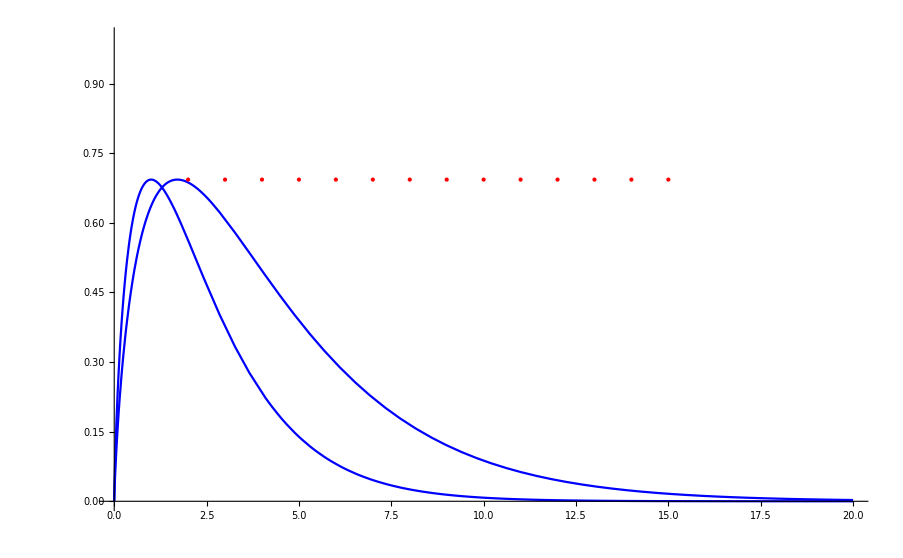

```mathematica
(*No attack*)
RP=RunningProbabilities[{{α, 1-α}, {0, 1}}, {1, 0}];
RP[t]
ep =(%//EntropyProcess)//FullSimplifyForPositiveReals
ep/.α->(T-1)/T
Show[Plot[Table[%, {T, 2, 3}], {t, 0, 20}, PlotStyle->Blue, PlotRange->{0, 1}], ListPlot[Table[{t, Log[2]}, {t, 2, 15}], PlotStyle->{Red,PointSize[Large]},Axes->None]]
```

```mathematica
D[ep, t]
```

```mathematica
Integrate[ep, {t, 0, Infinity}]
```

ConditionalExpression[-π^2/(6 Log[α]), Re[Log[α]]<0]

```mathematica
-α^t Log[α]-(α^t (-1+α^t) Log[α])/(1-α^t)-t α^t Log[α]^2+α^t Log[α] Log[1-α^t]/.α->1/7
```

7^-t Log[7]+(7^-t (-1+7^-t) Log[7])/(1-7^-t)-7^-t t Log[7]^2-7^-t Log[7] Log[1-7^-t]

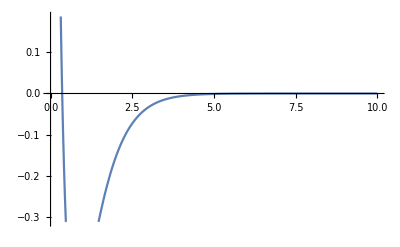

```mathematica
Plot[7^-t Log[7]+(7^-t (-1+7^-t) Log[7])/(1-7^-t)-7^-t t Log[7]^2-7^-t Log[7] Log[1-7^-t],{t, 0, 10}]
```